```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/kenneth_levasseur/Library/Mobile Documents/com~apple~CloudDocs/Documents/ps/images

```mathematica
f[x_]:=Log[1+x^2]
```

```mathematica
a=0.75;
g[x_]:=f[x]-a x
```

```mathematica
{rm,rp}=x/.Solve[2x/(1+x^2)==a,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.451416,2.21525}

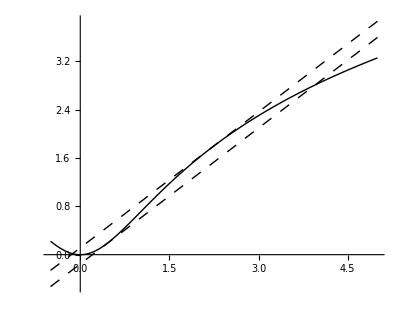

```mathematica
p=Plot[{f[x],a x +g[rm],a x + g[rp]},{x,-0.5,5},AspectRatio->Automatic,PlotStyle->{{Black,Thin},{Black,Thin,Dashing[{0.02,0.02}]},{Black,Thin,Dashing[{0.02,0.02}]}}]
```

```mathematica
Export["fig_2022A1.png",p,"PNG"]
```

fig_2022A1.png